# Seminarska naloga za ROM - Maturitetne naloge

## 1. Risanje grafov

a)    Narišite graf funkcije f(x)= 1/x.

Da narišemo graf, bomo funkcijo na določenemu intervalu vstavili v Plot.

1/x

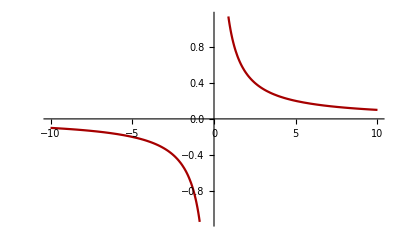

```mathematica
f[x_] = 1 /x
Plot[f[x],{x,-10,10}]
```

Odgovor: Je prikazan kot narisan graf

1.b) Zapišite enačbo tangente na graf funkcije f v točki z absciso x0 = 1/2, ter jo nariši

```mathematica
D[f[x],x]
```

-1/x^2

```mathematica
ClearAll[b]
tangenta[x0_,gr_]:= Module[{k,n},
k= D[gr[b],b]/.{b->x0};
n= p/.Solve[f[x0]==k*x0+p,p];
k*x+n
]
```

```mathematica
odvod[x_]=D[f[x],x]
```

-1/x^2

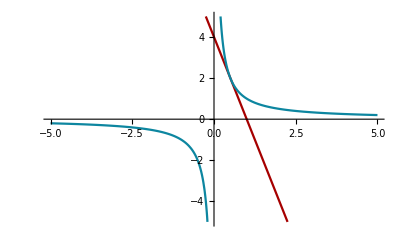

```mathematica
Plot[{tangenta[1/2,f],f[x]},{x,-5,5},PlotRange->{-5,5}]
```

```mathematica
Manipulate[Plot[{tangenta[x0,f],f[x]},{x,-5,5},PlotRange->{-5,5}],{x0,-4,4}]
```

Odgovor: Je prikazan kot narisan graf ter za radovedneže sem dodal še Manipulate tako, da lahko vidimo kako se tangenta giba po grafu.

## 2. Računanje integralov

### Na sliki je graf zvezne funkcije f , ki ima natanko tri ničle: x0 = 0, x1 = 2 ter x2 = 5. Ploščina, ki ga omejujeta graf funkcije f in abscisna os na intervalu [0, 2] je S1 = 1,3. Ploščina ki ga omejujeta graf funkcije f in abscisna os na intervalu [2, 5 ,] je S2 = 3,9 (glejte sliko).

S slike preberite ali izračunajte določene integrale:


		
		
		
		Ker je na maturitetni nalogi graf bil že narisan sem se odločil, da ga bom še sam narisal za boljši prikaz.

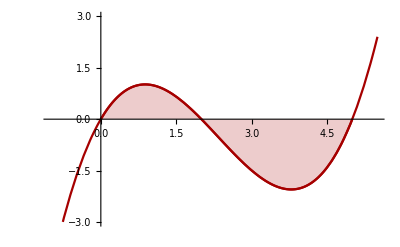

```mathematica
g[x_]:= 1/4x*(x-2)*(x-5)
Show[
Plot[g[x],{x,-1,5.5},PlotRange->{-3,3}],
Plot[g[x],{x,0,5},PlotRange->{-10,10},Filling->Axis]
	]
```

S slike  izračunajte določene integrale:

```mathematica
integral[t_,z_]:=N[Integrate[t,z],3]
integral[g[x],{x,0,2}]
integral[g[x],{x,2,5}]
integral[g[x],{x,0,5}]
integral[4*g[x],{x,0,2}]
integral[g[x]+2x^2,{x,2,5}]
integral[g[x-1],{x,1,3}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {3,0,2}.

NIntegrate::itraw: Raw object 3 cannot be used as an iterator.

NIntegrate::itraw: Raw object 3. cannot be used as an iterator.

NIntegrate[-1.5,{3.,0,2.},WorkingPrecision→16.,AccuracyGoal→∞,PrecisionGoal→6.]

Integrate::ilim: Invalid integration variable or limit(s) in {3,2,5}.

NIntegrate::itraw: Raw object 3 cannot be used as an iterator.

NIntegrate::itraw: Raw object 3. cannot be used as an iterator.

NIntegrate[-1.5,{3.,2.,5.},WorkingPrecision→16.,AccuracyGoal→∞,PrecisionGoal→6.]

Integrate::ilim: Invalid integration variable or limit(s) in {3,0,5}.

NIntegrate::itraw: Raw object 3 cannot be used as an iterator.

NIntegrate::itraw: Raw object 3. cannot be used as an iterator.

NIntegrate[-1.5,{3.,0,5.},WorkingPrecision→16.,AccuracyGoal→∞,PrecisionGoal→6.]

Integrate::ilim: Invalid integration variable or limit(s) in {3,0,2}.

NIntegrate::itraw: Raw object 3 cannot be used as an iterator.

NIntegrate::itraw: Raw object 3. cannot be used as an iterator.

NIntegrate[-6.,{3.,0,2.},WorkingPrecision→16.,AccuracyGoal→∞,PrecisionGoal→6.]

Integrate::ilim: Invalid integration variable or limit(s) in {3,2,5}.

NIntegrate::itraw: Raw object 3 cannot be used as an iterator.

NIntegrate::itraw: Raw object 3. cannot be used as an iterator.

NIntegrate[16.5,{3.,2.,5.},WorkingPrecision→16.,AccuracyGoal→∞,PrecisionGoal→6.]

Integrate::ilim: Invalid integration variable or limit(s) in {3,1,3}.

NIntegrate::itraw: Raw object 3 cannot be used as an iterator.

NIntegrate::itraw: Raw object 3. cannot be used as an iterator.

NIntegrate[0,{3.,1.,3.},WorkingPrecision→16.,AccuracyGoal→∞,PrecisionGoal→6.]

Odgovor: So sledeča števila:  1.33,  -3.94,  -2.6,  5.3,3  74.1,  1.33

## 3. Risanje Stožnic

#### Dan je pravokotnik ABCD z oglišči A( -3 , -2 ), B( 3 , -2 ),C( 3 , 2 )in D ( -3 , 2 ). a) Zapišite enačbo elipse v središčni legi,ki je včrtana v pravokotnik ABCD in se dotika vseh štirih njegovih stranic. b) Zapišite enačbo hiperbole v središčni legi, ki ima teme v točki T(0, 2 ) njeni asimptoti pa sta nosilki diagonal pravokotnika ABCD c) Zapišite enačbo krožnice, ki ima središče v točki C in poteka skozi točko A.

Zaradi lažjega prikaza ter nazora sem vse tri naloge dal na eno ravnino ter tudi pravokotnik sem naredil z funkcijo Countour Plot.

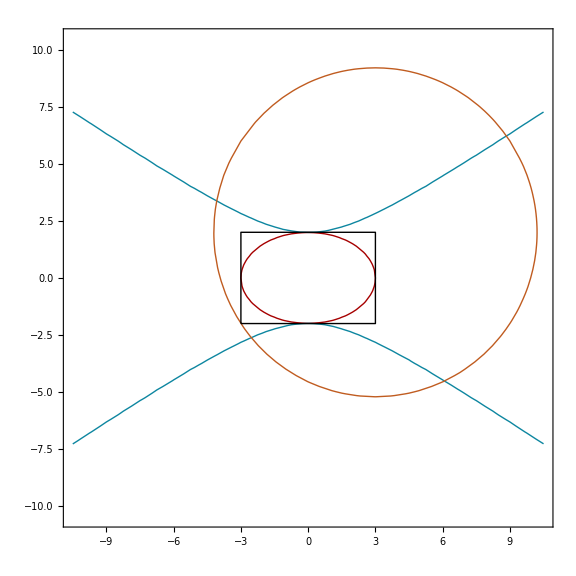

```mathematica
Show[
ContourPlot[{x^2/3^2+y^2/2^2==1,x^2/3^2-y^2/2^2==-1,(x-3)^2+(y-2)^2==52},{x,-10.5,10.5},{y,-10.5,10.5}],
Graphics[Line[{{-3,-2},{3,-2},{3,-2},{3,2},{3,2},{-3,2},{-3,2},{-3,-2}}]]
]
```

Odgovor: So zgornje narisane krivulje.

## 4. Največji skupni delitelj ,najmanjši skupini večkratnik in razcep številna prafaktorje

### Za poljubni naravni števili m in n označimo z D (m, n ) največji skupni delitelj teh dveh števil in z v (m, n ) njun najmanjši skupini večkratnik. a) Razcepite števila 45, 48 in 60 na prafaktorje.

```mathematica
ClearAll[a,b,c]
Prafaktorizacija[x_]:=FactorInteger[x]
a = 45
b = 48
c = 60
Prafaktorizacija[a]
Prafaktorizacija[b]
Prafaktorizacija[c]
```

45

48

60

{{3,2},{5,1}}

{{2,4},{3,1}}

{{2,2},{3,1},{5,1}}

#### b) Izračunajte : (D(45,48)/D(48,60) - D(11,23)/v(4, 10)) * v(5,20)

```mathematica
ClearAll[x,y,z,t]
NajvecjiSkupniDeljitelj[x_,y_]:=GCD[x,y]
NajmanjsiSkupniVečkratnik[t_,z_]:= LCM[t,z]

a =NajvecjiSkupniDeljitelj[45,48]
b= NajvecjiSkupniDeljitelj[48,60]
c=NajvecjiSkupniDeljitelj[11,23]
d=NajmanjsiSkupniVečkratnik[4,10]
e=NajmanjsiSkupniVečkratnik[5,20]

Rezultat =(FractionBox[a,b]-FractionBox[c,d])*e
```

3

12

1

20

20

20 (-FractionBox[1,20]+FractionBox[3,12])

```mathematica
20 (-FractionBox[1,20]+FractionBox[3,12])OverBar[■]
Rezultat
```

20 (-FractionBox[1,20]+FractionBox[3,12]) OverBar[■]

20 (-FractionBox[1,20]+FractionBox[3,12])

Odgovor: Rešitev sledečih nalog so 45, 48 ,60; ter od naloge

## 5. Računanje nedoločenega integrala

#### Izračunajte nedoločeni integral ∫((2 x^2-3)/x+(x^2)^(1/3)-e^x+5)ⅆx.

```mathematica
ClearAll[x]
```

```mathematica
Integrate[(2x^2-3)-3+CubeRoot[x^2]-E^x+5,x]
```

-ⅇ^x-x+(2 x^3)/3+3/5 x (x^2)^(1/3)

Odgovor: Rešitev te naloge je-ⅇ^x-x+(2 x^3)/3+3/5 x (x^2)^(1/3)

## 6. Vektorji

V prostoru R^3 so dani vektorji a = (1, 2,- 1)  , b =  (x, -2, -1)  in c = (1, 1, 2)  .

a)  Računsko pokažite, da sta vektorja a in b pravokotna in izračunaj x.

```mathematica
ClearAll[x,a,b,c]

a = {1,2,-1}
b = {x,-2,-1}
c = {1,1,2}
```

{1,2,-1}

{x,-2,-1}

{1,1,2}

```mathematica
Solve[Dot[a,b] ==0,x]
```

{{x→3}}

Odgovor: x je 3.

### b) Izračunaj vektorski produkt od b in c.

```mathematica
x = 3
Cross[{x,-2,-1},{1,1,2}]
```

3

{-3,-7,5}

Odgovor: Vektorski produkt je {-3,-7,5}.

### c) Izračunaj 3a + 4b - c/2.

```mathematica
Simplify[3*a+4*b-c/2]
```

{29/2,-5/2,-8}

Odgovor je{29/2,-5/2,-8}.

### d) Izračunaj Normo danih vektorjev.

```mathematica
Norm[a]
Norm[b]
Norm[c]
```

√6

√14

√6

Odgovor: Dolžine vektorje √6, √14 in √6.

## 7. Kvadratne enačbe in Diskriminante

Izračunajte diskriminante in poiščite vse rešitve kvadratnih enačb. Rezultate zapišite v preglednico. 

Ker je v nalogi bila že podana tabela, sem se v tem primeru da bom še sam naredil tabelo ter jo sproti izpolnjeval.

```mathematica
ClearAll[x,a,b,c,d,e,f,p,o,h,j,z,u]
Diskriminanta[a_,b_,c_]:=b^2-4*a*c
DiskriminantaPrveEnačbe=Diskriminanta[1,-6,9]
DiskriminantaDrugeEnačbe=Diskriminanta[1,-3,-10]
DiskriminantaTretjeEnačbe=Diskriminanta[1,-6,10]

RešitveEnačbe1[a_,b_,c_]:=-b+Sqrt[b^2-4*a*c]
RešitveEnačbe2[a_,b_,c_]:=-b-Sqrt[b^2-4*a*c]

RešitvePrveEnačbe1=RešitveEnačbe1[1,-6,9]
RešitvePrveEnačbe2=RešitveEnačbe2[1,-6,9]
RešitveDrugeEnačbe1=RešitveEnačbe1[1,-3,-10]
RešitveDrugeEnačbe2=RešitveEnačbe2[1,-3,-10]
RešitveTretjeEnačbe1=RešitveEnačbe1[1,-6,10]
RešitveTretjeEnačbe2=RešitveEnačbe2[1,-6,10]
```

0

49

-4

6

6

10

-4

6+2 ⅈ

6-2 ⅈ

```mathematica
Grid[{{"x^2 +6x+9=0",a,b},{"x^2-3x-10=0",d,e},{"x^2-6x+10=0",g,g}}]
```

x^2 +6x+9=0 | a | b
x^2-3x-10=0 | d | e
x^2-6x+10=0 | g | g

```mathematica
Insert[Grid[{{"x^2 +6x+9=0",DiskriminantaPrveEnačbe,RešitvePrveEnačbe1,RešitvePrveEnačbe2},{"x^2-3x-10=0",DiskriminantaDrugeEnačbe,RešitveDrugeEnačbe1,RešitveDrugeEnačbe2},{"x^2-6x+10=0",DiskriminantaTretjeEnačbe,RešitveTretjeEnačbe1,RešitveTretjeEnačbe2}}],{Dividers->All,Spacings->1.5 {1,1}},2]
```

x^2 +6x+9=0 | 0 | 6 | 6
x^2-3x-10=0 | 49 | 10 | -4
x^2-6x+10=0 | -4 | 6+2 ⅈ | 6-2 ⅈ

```mathematica
ReplacePart[Grid[{{"x^2 +6x+9=0",0,6,6},{"x^2-3x-10=0",49,10,-4},{"x^2-6x+10=0",-4,6+2 ⅈ,6-2 ⅈ}},{Dividers->All,Spacings->{1.5,1.5}}],1->Prepend[First[Grid[{{"x^2 +6x+9=0",0,6,6},{"x^2-3x-10=0",49,10,-4},{"x^2-6x+10=0",-4,6+2 ⅈ,6-2 ⅈ}},{Dividers->All,Spacings->{1.5,1.5}}]],{"Enačba","Diskriminanta","Prva rešitev enačbe","Druga rešitev enačbe"}]]
```

Enačba | Diskriminanta | Prva rešitev enačbe | Druga rešitev enačbe
x^2 +6x+9=0 | 0 | 6 | 6
x^2-3x-10=0 | 49 | 10 | -4
x^2-6x+10=0 | -4 | 6+2 ⅈ | 6-2 ⅈ

Odgovor: Odgovori so podani v tabeli


Tukaj sem se odločil za maximalen prikaz zato sem dodal še imena stoplcem.

Zaradi kvadratne enačbe dobimo dve rešitvi in tako sem tudi naredil dva stoplca za obe rešitvi.